# Numerical ODE Solvers: RK45 and Details

The solver lots of matlab users suggest as a default solver is ode45.  ODE 45 is an explicit RK scheme using the Dormand-Prince RK pair with tableau.  The orders of the schemes should be 5 and 4 if I typed the coefficients correctly.

```mathematica
DormandPrinceTableau={
({{0, 0, 0, 0, 0, 0, 0}, {1/5, 0, 0, 0, 0, 0, 0}, {3/40, 9/40, 0, 0, 0, 0, 0}, {44/45, -56/15, 32/9, 0, 0, 0, 0}, {19372/6561, -25360/2187, 64448/6561, -212/729, 0, 0, 0}, {9017/3168, -355/33, 46732/5247, 49/176, -5103/18656, 0, 0}, {35/384, 0, 500/1113, 125/192, -2187/6784, 11/84, 0}}),
{35/384,0,500/1113,125/192,-2187/6784,11/84,0},
{5179/57600, 0, 7571/16695,393/640,-92097/339200,187/2100,1/40}};
RK2B[f_,{A_List,b_List,bStar_List}][{h_,t_,y_}]:=Module[{k=Length[A],Ks},
(* Compute Internal Slopes *)
Ks[1]=f[y];
Do[
Ks[i]=f[y+h*Sum[A⟦i,j⟧ Ks[j],{j,1,i-1}]],
{i,1,k}];
(* Returning the better and OK approximations *)
{y+h*Sum[b⟦i⟧ Ks[i],{i,1,k}],y+h*Sum[bStar⟦i⟧ Ks[i],{i,1,k}]}
]
```

Lets test to see if the coefficients are all correct.  Looks like the errors are small but are they as small as they are supposed to be?

```mathematica
Clear[f,y]
f[y_]:=y
{t0,y0}={0.0,1.0};
h=0.2;
RK2B[f,DormandPrinceTableau][{h,t0,y0}]-E^h
```

{1.51732×10^-8,2.53573×10^-7}

Lets make a picture and see how things behave with h. Remember all we really care about is the order. In other words we only care about the power of h!

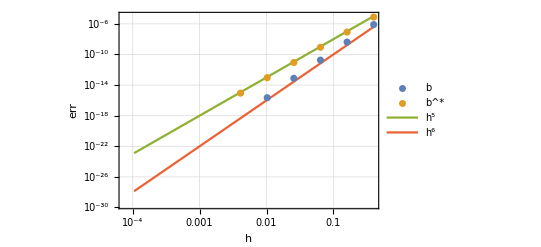

```mathematica
hList=Table[0.4^i,{i,1,10}];
{bErrs,bStarErrs}=Table[ Abs[RK2B[f,DormandPrinceTableau][{h,t0,y0}]-E^h],{h,hList}]ᵀ;ListLogLogPlot[{{hList,bErrs}ᵀ,{hList,bStarErrs}ᵀ,
01{hList,0.001 hList^5}ᵀ,{hList,0.0001 hList^6}ᵀ},
Joined->{False,False,True,True,True,True},
GridLines->Automatic,Frame->True,FrameLabel->{"h","err"},
PlotLegends->{"b","b^*","h^5","h^6"},PlotRange->All]
```

This is another way to check for typos.  We can see that the better “b” scheme has order 5 since its single step error matches C h^(5+1). We can see that the OK "b^*" scheme has order 4 since its single step error matches Ĉ h^(4+1). We can also see that we can take substantially larger steps with these “fancy” solvers.

This is a very standard moderate precision solver used in Python and Julia and simulink.  It is also an available option in NDSolve.  Why rare there lots of other solvers?  This is pretty uch the same question as what can go wrong?

## Stiff Equations

There is one particular common type of system that explicit solvers struggle with.  This sort of system is called “stiff” and we will see a definition in a bit.  The “diagnostic” symptom that your system is probably stiff in matlab or Python etc. is that it takes tiny steps for no obvious reason!  In Mathematica if you force a bad choice you get a better error message.  Here is an example.

```mathematica
A={
{-1002.0,-1000},
{-1000,-1001}};
ySolRK= NDSolveValue[{y'[t]==A.y[t],y[0]=={0.1,0.4}},y,{t,0,1},
Method->"ExplicitRungeKutta"]
```

NDSolveValue::ndstf: At t == 0.0184712, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

InterpolatingFunction[…]

If you let Mathematica choose you just get an answer!

InterpolatingFunction[…]

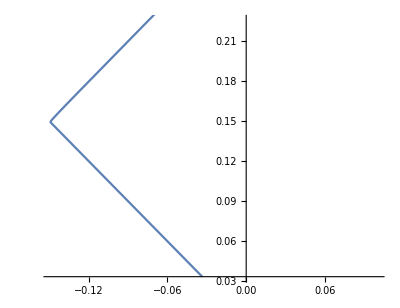

```mathematica
ySol= NDSolveValue[{y'[t]==A.y[t],y[0]=={0.1,0.4}},y,{t,0,1}]
ParametricPlot[ySol[t],{t,0,1},PlotPoints->100]
```

The big question is why is this problem hard?  How does Mathematica know it is stiff and what does it use instead of an Explicit RK Scheme?

## Interpolation and Dense Output

The schemes we have looked at produce values (and derivatives) at a sequence of points.  The variable step size stuff lets us take appropriately sized steps but it does not change the “dotty” nature of the approximate solution.  Mathematica joins the points up using “standard” interpolation.  Standard interpolations are not as accurate as standard ODE solvers.  This is easily visualizable.

```mathematica
ySol["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

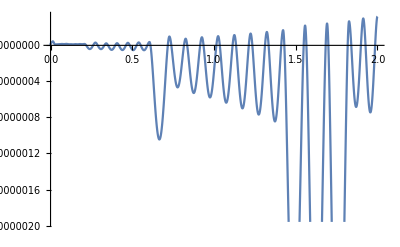

```mathematica
TMax=2;
ySol=NDSolveValue[{y'[t]==y[t],y[0]==1},y,{t,0,TMax}];
Plot[ySol[t]-E^t,{t,0,TMax}]
```

You can ask Mma what sorts of things you can do with an interpolating function.

```mathematica
ySol["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}